```mathematica
Valuation[n_,p_]:=Valuation[n,p]=IntegerExponent[Abs[Numerator[n]],p]-IntegerExponent[Denominator[n],p]
```

```mathematica
SetAttributes[Valuation,Listable]
```

```mathematica
Valuation[{1,{2,4,8},3,4,5},2]
```

{0,{1,2,3},0,2,0}

```mathematica
Grid[Valuation[Table[Binomial[n,k],{n,0,10},{k,0,n}],2]]
```

0 |  |  |  |  |  |  |  |  |  | 
0 | 0 |  |  |  |  |  |  |  |  | 
0 | 1 | 0 |  |  |  |  |  |  |  | 
0 | 0 | 0 | 0 |  |  |  |  |  |  | 
0 | 2 | 1 | 2 | 0 |  |  |  |  |  | 
0 | 0 | 1 | 1 | 0 | 0 |  |  |  |  | 
0 | 1 | 0 | 2 | 0 | 1 | 0 |  |  |  | 
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 |  |  | 
0 | 3 | 2 | 3 | 1 | 3 | 2 | 3 | 0 |  | 
0 | 0 | 2 | 2 | 1 | 1 | 2 | 2 | 0 | 0 | 
0 | 1 | 0 | 3 | 1 | 2 | 1 | 3 | 0 | 1 | 0

```mathematica
LRPValSymmetry[F_,rows_,p_]:=
ArrayPlot[
Valuation[
Table[
PadLeft[
Riffle[
Table[
F[n,k],
{k,0,n}],
0],2rows+1,0,Floor[(rows-n)]
],
{n,0,rows}],
p]
,ImageSize->1000]
```

```mathematica
Manipulate[LRPValSymmetry[Binomial[#1,#2]^m&,rows,p],{m,1},{p}]
```

```mathematica
Manipulate[ListLinePlot[Table[Valuation[Sum[Binomial[n,k]^m,{k,0,n}],p],{n,0,rows}]],{p,2},{rows,10},{m,1}]
```

```mathematica
BinomPower[n_,power_]:=Sum[Binomial[n,k]^power,{k,0,n}]
```

```mathematica
ListValPlot[F_,p_,range_]:=ListLinePlot[Table[Valuation[F[n],p],{n,1,range}]]
```

```mathematica
Manipulate[
ArrayPlot[Table[
PadLeft[Riffle[
Table[
Valuation[Sum[
Binomial[n,k],
{k,0,column}],p],
{column,0,n}],
""],2rows+1,"",rows-n]
,{n,0,rows}]
,ImageSize-> 1000],{rows,10},{m,2},{p,2}]
```

```mathematica
Derangements[n_]:= n!Sum[(-1)^k/(k!),{k,2,n}]
```

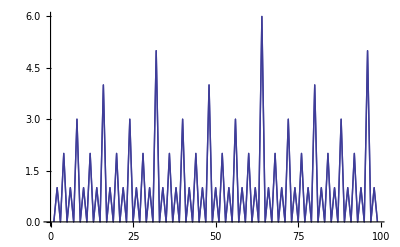

```mathematica
Show[ListLinePlot[Valuation[Table[Derangements[n],{n,2,100}],2]],ListLinePlot[Valuation[Table[n-1,{n,2,100}],2]]]
```

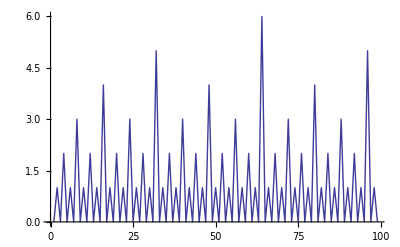
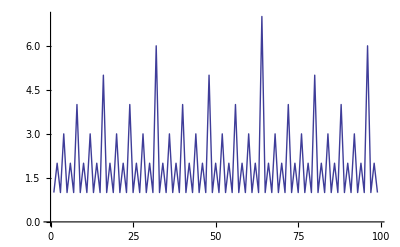
-Graphics-==-Graphics-

```mathematica
ListLinePlot[Valuation[Table[Derangements[n],{n,2,100}],2]]==ListLinePlot[Valuation[Table[2(n-1),{n,2,100}],2]]
```

```mathematica
Manipulate[Show[ListLinePlot[Valuation[Table[Derangements[n],{n,2,range}],p]],ListLinePlot[Valuation[Table[n-1,{n,2,range}],p]]],{range,100},{p,2}]
```